# CCBH and Power Law + Peak: Formation PDF

Davi  C. Rodrigues (this code). July, 2023.

```mathematica
ResourceFunction["DarkMode"][]
```

CCBH = Cosmologically coupled black hole (general case)
DEBH = Dark energy coupled Black Hole (implies k = - 3w)
GBH = Growing BH, k is arbitrary and without direct dark energy impact.
m1 = primary (larger) mass of the BBH or NSBH pair.


Naming conventions:
All defined variables/functions start with lower case letter.
“I" at the end of a function name: interpolated version. 
"Raw”: a function without options. It is useful to store results. The version with options is based on the raw version.

## Starting...

```mathematica
SetDirectory[NotebookDirectory[]];
Get[FileNameJoin[{"codes", "Directories.wl"}]];

(*
  Calling wl files
  ***************** 
*)
getCode["Constants.wl"];
baseSimPoints = 10^7; (*The base number of points to be simmulated for each dimension, commonly 10^5-10^7, depends on the purpose.*)

getCode["ObsDataPreparationGWTC-3.wl"]; (*Not essential for this notebook*)
getCode["PowerLawPlusPeakDefinition.wl"];
getCode["Cosmology.wl"];
getCode["MassFactorCorrection.wl"];

Print["End of running wl files."];

(*
  GENERAL PURPOSE FUNCTIONS
  **************************
*)

findSigma::usage = "findSigma[probability] yields the number of σ's for a given probability.";
findSigma[prob_] := Block[{sigma}, 
  sigma /. FindRoot[NProbability[Abs[x] > sigma , x\[Distributed]NormalDistribution[]] == prob, {sigma, 2}]
];

Clear[outSigma];
outSigma[n_] := outSigma[n] = NProbability[Abs[x] > n, x\[Distributed]NormalDistribution[]];
```

Starting Constants.wl:

Starting ObsDataPreparationGWTC-3.wl:

Number of m1 black holes:   72

Starting PowerLawPlusPeakDefinition.wl:

Use plpp`pi[m, options] for the power-law-plus-peak PDF and plpp`𝒟[options] for the distribution. Use optionsPlpp to see the options.

Starting Cosmology.wl:

tableZformation loaded.

Starting MassFactorCorrection.wl:

Base number of simmulated points per dimension (baseSimPoints):   10000000

"dataM1Merger"  51.2913

End of running wl files.

## Table and plot on observational data

```mathematica
eventsNames = datasetGWTrelev // Keys // Normal;
tablePaper = {#1, #2, #3, #5} & @@@  (Join[{eventsNames},mXzDataForPlotting1ᵀ, mXzDataForPlotting2ᵀ]ᵀ);
%[[1;;5]] // TeXForm
(* exportOut["dataGWexport.csv", dataGWexport]; *)
```

\left(
\begin{array}{cccc}
 \text{GW150914} & 0.090_{-0.030}^{+0.030} & 35.6_{-3.1}^{+5.} & 30.6_{-4.}^{+3.0} \\
 \text{GW151012} & 0.21_{-0.09}^{+0.09} & 23._{-6.}^{+15.} & 14._{-5.}^{+4.} \\
 \text{GW151226} & 0.09_{-0.04}^{+0.04} & 13.7_{-3.2}^{+9.} & 7.7_{-2.5}^{+2.2} \\
 \text{GW170104} & 0.20_{-0.08}^{+0.08} & 31._{-6.}^{+7.} & 20._{-5.}^{+5.} \\
 \text{GW170608} & 0.070_{-0.020}^{+0.020} & 11.0_{-1.7}^{+6.} & 7.6_{-2.2}^{+1.4} \\
\end{array}
\right)

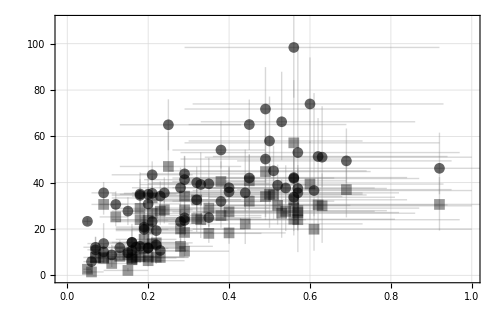

```mathematica
plotZxM12 = ListPlot[{mXzDataForPlotting1, mXzDataForPlotting2},
  IntervalMarkersStyle -> {{Opacity[0.3], Gray}, {Opacity[0.3],Gray}},
  PlotRange-> {{-0.01,1.0},{-1, 110}},
  PlotRange->All, 
  Axes -> False, 
  Frame -> True, 
  PlotMarkers->{Graphics[{Black, Opacity[0.6],Disk[]}, ImageSize -> 11, ImagePadding->1], Graphics[{Black, Opacity[0.4], Rectangle[]}, ImageSize -> 11, ImagePadding->1]}, 
  IntervalMarkersStyle-> {Opacity[0.5],Darker@Blue},
  ImageSize->500, 
  GridLines->Automatic, 
  GridLinesStyle->Dotted,
  FrameTicksStyle->Directive[FontFamily->"Times New Roman",FontSize->17, FontColor -> "Black"],
  Background -> White]
```

```mathematica
exportOut["plotZxM12.pdf", plotZxM12]
```

pathOut/plotZxM12.pdf

## Verification of zFormationI

Inspecting the computed points and the interpolation

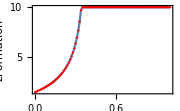
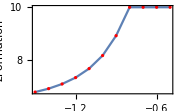
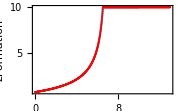
Visually checking the interpolation:   -Graphics--Graphics--Graphics-

```mathematica
originalPlotOptions = Options[Plot];
SetOptions[Plot, Frame -> True, Axes -> False, PlotRange -> All];

Echo[
  Row[{
    Show[
      Plot[zFormationI[zObs, 9, zMax0, w0], 
        {zObs, 0.05, 1.0}, 
        FrameLabel->{"zObs", "zFormation"}
      ], 
      ListPlot[{#, zFormation[#, 9, zMax0, w0]} & /@ listzObs, PlotStyle->Red],
      ImageSize -> Small
    ],
    Show[
      Plot[zFormationI[1, 5, zMax0, w1], 
        {w1, -1.5, -0.5}, 
        FrameLabel->{"w", "zFormation"}
      ], 
      ListPlot[{#, zFormation[1, 5, zMax0, #]} & /@ listw, PlotStyle->Red],
      ImageSize -> Small
    ],
    Show[
      Plot[zFormationI[0.7, delayTime, zMax0, w0], 
        {delayTime, 0.1, 10}, 
        FrameLabel->{"t_d", "zFormation"}
      ], 
      ListPlot[{#, zFormation[0.7, #, zMax0, w0]} & /@ listDelayTime, PlotStyle->Red],
      ImageSize -> Small
    ]
  }],
  "Visually checking the interpolation: "
];
SetOptions[Plot, originalPlotOptions];
```

## The mass factor distribution (𝒟MassFactor & 𝒟InvMassFactor)

ATTENTION: 𝒟MassFactor and dataMassFactor do not work well under paralelization. This is a known issue with computing interpolated function in parallel, and they depend on zFormationI. If zFormatino is used in place, the parallelization works fine, but the improvement of using zFormationI is a factor of ~100, thus parallelizing is not worth. To avoid the issue, I tried doing the interpolatin in the subkernels, but there was no relevant improvement. So I stopped trying to parallel these functions.

```mathematica
ClearAll[
  𝒟MassFactor,
  𝒟InvMassFactor
];

𝒟MassFactor[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := 𝒟MassFactor[zObs, tdmin, tdmax, k, zMax, w] = SmoothKernelDistribution[
  dataMassFactor[zObs, tdmin, tdmax, k, zMax, w], 
  0.001 (*Manual selection of the band, leads to 0.1% maximum mass precision. Silverman leads to 0.06 for the bandwidth, SheaterJones takes a lot of time and does not converge.*), 
  InterpolationPoints -> 10^4, 
  MaxExtraBandwidths -> {0,0}, 
  PerformanceGoal->"Quality"
];

𝒟InvMassFactor[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := 𝒟InvMassFactor[zObs, tdmin, tdmax, k, zMax, w] = SmoothKernelDistribution[
  1/dataMassFactor[zObs, tdmin, tdmax, k, zMax, w], 
  0.001 (*Manual selection of the band, leads to 0.1% maximum mass precision. Silverman leads to 0.06 for the bandwidth, SheaterJones takes a lot of time and does not converge.*), 
  InterpolationPoints -> 10^4, 
  MaxExtraBandwidths -> {0,0}, 
  PerformanceGoal->"Quality"
];
```

#### 𝒟InvMassFactor plots

```mathematica
isCompute𝒟MassFactorCases = False; (*Saved with 2 10^6 realizations*) 

If[isCompute𝒟MassFactorCases, 
  Echo["Computing 𝒟MassFactor 0.05 and 0.9 cases..."];
  𝒟InvMassFactor005 = 𝒟InvMassFactor[0.05, tdmin0, tdmax0, k0, zMax0, w0]; // EchoTiming;
  𝒟InvMassFactor09 = 𝒟InvMassFactor[0.9, tdmin0, tdmax0, k0, zMax0, w0]; // EchoTiming; (*Issue: parallelizing here has several issues, it is quicker this way.*)
  dumpsave["DInvMassFactor005.mx", 𝒟InvMassFactor005];
  dumpsave["DInvMassFactor09.mx", 𝒟InvMassFactor09],
  (*else*)
  getAux["DInvMassFactor005.mx"];
  getAux["DInvMassFactor09.mx"];
  𝒟InvMassFactor[0.05, tdmin0, tdmax0, k0, zMax0, w0] = 𝒟InvMassFactor005;
  𝒟InvMassFactor[0.9, tdmin0, tdmax0, k0, zMax0, w0] = 𝒟InvMassFactor09;
  Echo["𝒟MassFactor 0.05 and 0.9 cases loaded."];
];
```

𝒟MassFactor 0.05 and 0.9 cases loaded.

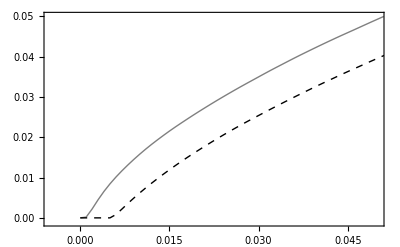

```mathematica
plotInverseMassFactorCDF = Block[{cdfValues1, cdfValues2},
  cdfValues1 = {#, CDF[𝒟InvMassFactor[0.05, tdmin0, tdmax0, k0, zMax0, w0], #]} & /@ Range[0,1,0.001];
  cdfValues2 = {#, CDF[𝒟InvMassFactor[0.9, tdmin0, tdmax0, k0, zMax0, w0], #]} & /@ Range[0,1,0.001];
  ListPlot[
    {cdfValues1, cdfValues2}, 
    Joined -> True, 
    PlotRange -> {{-0.005,0.05}, {-0.001, 0.05}},
    Frame-> True,
    Axes -> False,
    Background->White,
    FrameStyle-> Directive[Black, FontSize -> 13],
    FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
    PlotStyle-> {{Thick, Gray}, {Thick, Dashed, Black}}
  ]
]
```

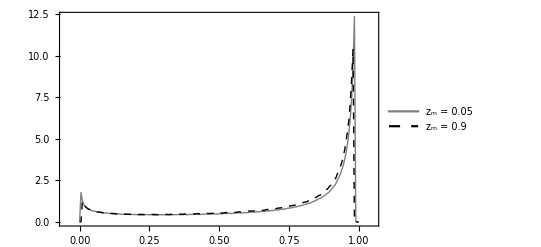

pathOut/plotInverseMassFactorDistribution2.pdf

```mathematica
plotInverseMassFactorDistribution = Block[{pdfValues1, pdfValues2},
  pdfValues1 = {#, PDF[𝒟InvMassFactor[0.05, tdmin0, tdmax0, k0, zMax0, w0], #]} & /@ Range[0,1,0.005];
  pdfValues2 = {#, PDF[𝒟InvMassFactor[0.9, tdmin0, tdmax0, k0, zMax0, w0], #]} & /@ Range[0,1,0.005];
  ListPlot[
    {pdfValues1, pdfValues2}, 
    Joined -> True, 
    PlotRange -> {{-0.05,1.05}, All},
    Frame-> True,
    Axes -> False,
    Background->White,
    FrameStyle-> Directive[Black, FontSize -> 13],
    FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
    PlotStyle-> {{Thick, Gray}, {Thick, Dashed, Black}},
    PlotLegends -> Placed[{
      Style["z_m = 0.05", FontFamily->"Times", FontSize -> 15], 
      Style["z_m = 0.9", FontFamily->"Times", FontSize -> 15]},
      {0.74, 0.88}
    ],
    Epilog -> Inset[plotInverseMassFactorCDF, {0.35, 6.2}, Automatic, Scaled[0.6] ]
  ]
]

exportOut["plotInverseMassFactorDistribution2.pdf", plotInverseMassFactorDistribution]
```

## Formation mass distribution

```mathematica
ClearAll[
  𝒟M1Formation, 
  𝒟M1FormationRaw
];

𝒟M1FormationRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := 𝒟M1FormationRaw[zObs, tdmin, tdmax, k, zMax, w] = SmoothKernelDistribution[
  dataM1FormationRaw[zObs, tdmin, tdmax, k, zMax, w],
  0.05, 
  InterpolationPoints -> 10^5, 
  MaxExtraBandwidths -> {2,2}, (*This slightly extends the profile beyond data (about 0.1 solar mass). 
  It is only used for the plot. Use {0,0} for no extension.*)
  PerformanceGoal->"Quality"
];

𝒟M1Formation[zObs_, opts:OptionsPattern[optionstkw]] := 𝒟M1FormationRaw[
  zObs, 
  OptionValue @ tdmin, 
  OptionValue @ tdmax, 
  OptionValue @ k, 
  OptionValue @ zMax, 
  OptionValue @ w
];
```

### Plots (Use ~10^7 data points)

This first plot probably will not get into the paper.

```mathematica
(*dataM1Formation[0.4]; //EchoTiming
dataM1Formation[0.4, k-> 0.5]; //EchoTiming
histFormation3 = Histogram[
  {dataM1Formation[0.4], dataM1Formation[0.4, k-> 0.5], dataM1Merger}, 
  {.2}, 
  "PDF", 
  PlotRange->{{0,50}, All},
  Background->White,
  ChartStyle->{Lighter@Orange, ColorData["AvocadoColors"][0.5], Lighter@Blue},
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  ChartLegends -> Placed[{
    Style["k = 3.0", FontFamily->"Times", FontSize -> 15], 
    Style["k = 0.5", FontFamily->"Times", FontSize -> 15], 
    Style["k = 0.0", FontFamily->"Times", FontSize -> 15]}, 
    {0.8, 0.75}
  ]
]

(*exportOut["histFormation3.pdf", histFormation3]*)*)
```

212.041

106.834

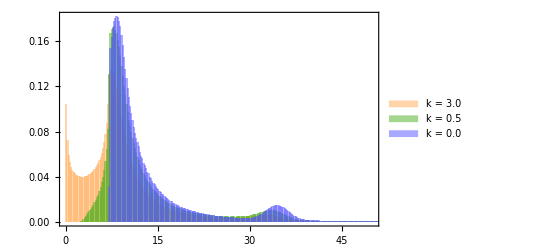

pathOut/histFormation3.pdf

```mathematica
tdmaxE = 5;
tdminE = 0.005;
zMaxE = 2;
𝒟M1Formation[0.4]; //EchoTiming
𝒟M1Formation[0.4, k-> 0.5]; //EchoTiming
𝒟M1Formation[0.4, tdmax -> tdmaxE]; //EchoTiming
𝒟M1Formation[0.4, tdmin -> tdminE]; //EchoTiming
𝒟M1Formation[0.4, zMax -> zMaxE]; //EchoTiming

legend1 = LineLegend[
  {Lighter@Orange, ColorData["AvocadoColors"][0.5], Lighter@Blue}, 
  {
    Style["k=3.0", FontFamily->"Times", FontSize -> 11], 
    Style["k=0.5", FontFamily->"Times", FontSize -> 11], 
    Style["k=0.0", FontFamily->"Times", FontSize -> 11]
  }, 
  LegendMarkerSize -> 20, 
  Spacings -> 0.15 (*It works, although in red*)
];

legend2 = LineLegend[
  {Directive[Lighter@Orange, Dashed], Directive[Lighter@Orange, Dotted], Directive[Lighter@Orange, DotDashed]}, 
  {
    Style["t_max=" <> ToString[Round@tdmaxE]<>" Gyr", FontFamily->"Times", FontSize -> 11], 
    Style["t_min=" <> ToString[Round[10^3 tdminE]]<>" Myr", FontFamily->"Times", FontSize -> 11],
    Style["z_max=" <> ToString[Round[zMaxE]], FontFamily->"Times", FontSize -> 11]
  }, 
  LegendMarkerSize -> 20, 
  Spacings -> 0.15 (*It works, although in red*)
];

tickLarge = 0.015;
tickSmall = 0.006;
frameTicksSmall = Flatten[Table[{n 10^i, "", tickSmall}, {n,1,10}, {i, -4, 0, 1}],1];
frameTicksLarge = Table[{10^i, Superscript[10, i], tickLarge}, {i, -4, 0, 1}];
frameTicksLargeDumb = Table[{10^i, "", tickLarge}, {i, -4, 0, 1}];
frameTicks = Flatten[Join[{frameTicksSmall, frameTicksLarge}],1];
frameTicksDumb = Flatten[Join[{frameTicksSmall, frameTicksLargeDumb}],1];


Off[General::munfl]; 
plotPDFformationDist = LogLogPlot[
  {
    PDF[𝒟M1Formation[0.4], x], 
    PDF[𝒟M1Formation[0.4, tdmax -> tdmaxE], x], 
    PDF[𝒟M1Formation[0.4, tdmin -> tdminE], x], 
    PDF[𝒟M1Formation[0.4, zMax -> zMaxE], x],
    PDF[𝒟M1Formation[0.4, k-> 0.5], x], 
    PDF[𝒟plp, x]
  }, 
  {x, 0.5, plpp`mMax /. optionsPlpp}, 
  PlotRange->{{0.5, 500}, {8 10^-5, .3}},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  FrameTicks->{{frameTicks, frameTicksDumb}, {Automatic, Automatic}},
  PlotPoints->5000,
  MaxRecursion->3,
  PlotStyle->{
    {Lighter@Orange}, 
    {Lighter@Orange, Dashed}, 
    {Lighter@Orange, Dotted}, 
    {Lighter@Orange, DotDashed}, 
    {ColorData["AvocadoColors"][0.5]}, 
    {Lighter@Blue}},
  PlotLegends-> {Placed[legend1, {0.60,0.81}], Placed[legend2, {0.85,0.81}]}
]
On[General::munfl];

exportOut["plotPDFformationDist.pdf", plotPDFformationDist]
```

2.15296

2.05971

0.983042

2.13426

2.02869

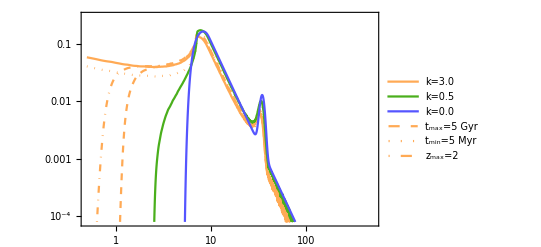

pathOut/plotPDFformationDist.pdf

## Probabilities for 2<m_th<5 (uses 10^7 Points) (EmpiricalCDF based)

m_th is the threshold mass.

### Computing the relevant distributions

```mathematica
𝒟M1FormationEmpRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := 𝒟M1FormationEmpRaw[zObs, tdmin, tdmax, k, zMax, w] = 
 EmpiricalDistribution[
   dataM1FormationRaw[zObs, tdmin, tdmax, k, zMax, w]
 ];

𝒟M1FormationEmp[zObs_, opts:OptionsPattern[optionstkw]] := 𝒟M1FormationEmpRaw[
  zObs, 
  OptionValue @ tdmin, 
  OptionValue @ tdmax, 
  OptionValue @ k, 
  OptionValue @ zMax, 
  OptionValue @ w
];

probabilityMminApprox[mMin_, opts:OptionsPattern[optionstkw]] := SurvivalFunction[𝒟M1FormationEmp[0.4, opts], mMin]^72;
probabilityMminDoubleApprox[mMin_, opts:OptionsPattern[optionstkw]] := SurvivalFunction[𝒟M1FormationEmp[0.4, opts], mMin]^(2*72);
```

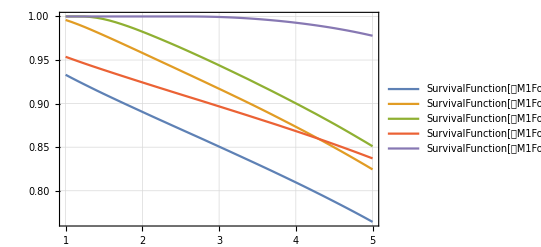

```mathematica
Plot[{
    SurvivalFunction[𝒟M1FormationEmp[0.4], x], 
    SurvivalFunction[𝒟M1FormationEmp[0.4, zMax -> zMaxE], x], 
    SurvivalFunction[𝒟M1FormationEmp[0.4, tdmax -> tdmaxE], x],
    SurvivalFunction[𝒟M1FormationEmp[0.4, tdmin -> tdminE], x],
    SurvivalFunction[𝒟M1FormationEmp[0.4, k -> 0.5], x]
  }, {x, 1, 5}, MaxRecursion->0, PlotRange->All, PlotTheme->"Detailed"]
```

```mathematica
Echo[{probabilityMminApprox[2], findSigma[probabilityMminApprox[2]]}, "Probability and tension level in sigmas, current data: "];
Echo[{probabilityMminDoubleApprox[2], findSigma[probabilityMminDoubleApprox[2]]}, "Probability and tension level in sigmas, future data: "];
```

Probability and tension level in sigmas, current data:   {0.000234232,3.67891}

Probability and tension level in sigmas, future data:   {5.48648×10^-8,5.43478}

### Probabilities related with minimum mass from the above distributions

Hence, with m_th = 2, the standard CCBH with k =3 is explided at more than 3 σ. Note that the approximation is quite good.

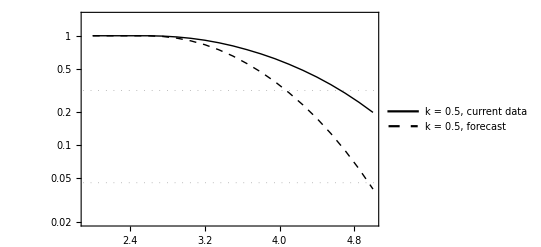

pathOut/plotProbabiliyNull005.pdf

```mathematica
frameTicksSmall = Flatten[Table[{n 10^i, "", tickSmall}, {n,1,10}, {i, -10, 0, 1}],1];
frameTicksLarge = Table[{10^i, Superscript[10, i], tickLarge}, {i, -10, 0, 1}];
frameTicks = Join[frameTicksSmall, frameTicksLarge];
tickLarge = 0.015;
tickSmall = 0.006;


plotProbabiliyNull005 = Block[
  {
    list = {#, probabilityMminApprox[#, k-> 0.5] } & /@ Range[2,5,0.15],
    list2 = {#, probabilityMminDoubleApprox[#, k-> 0.5] } & /@ Range[2,5,0.15]
  },
  ListLogPlot[{list, list2}, 
    Joined->True,
    PlotStyle->{{Thick, Black}, {Thick, Black, Dashed}},
    Background->White,
    Frame -> True,
    Axes -> False,
    FrameStyle-> Directive[Black, FontSize -> 13],
    FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
    FrameTicks->{{frameTicks, {{outSigma[1], "1σ"}, {outSigma[2], "2σ"}, {outSigma[3], "3σ"}}}, {Automatic, Automatic}},
    GridLines->{None, {outSigma[1], outSigma[2], outSigma[3]}},
    GridLinesStyle->Directive[Gray, Dotted],
    PlotLegends-> Placed[
      {Style["k = 0.5, current data", FontFamily->"Times", FontSize -> 14], Style["k = 0.5, forecast", FontFamily->"Times", FontSize -> 14]}, 
      {0.3,0.3}
    ],
    PlotRange->{All, {2 10^-2, 1.5}}
  ]
]

exportOut["plotProbabiliyNull005.pdf", plotProbabiliyNull005]
```

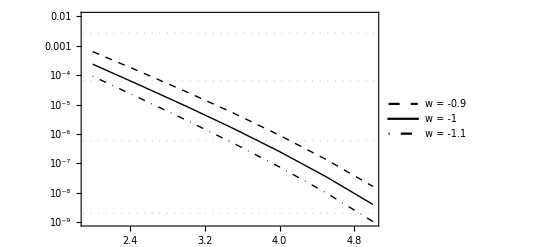

pathOut/plotProbabilityNullw.pdf

```mathematica
list1 = {#, probabilityMminApprox[#]} & /@ Range[2,5,0.5];
list2 = {#, probabilityMminApprox[#, k-> 3 0.9 , w-> -0.9]} & /@ Range[2,5,0.5];
list3 = {#, probabilityMminApprox[#, k-> 3 1.1 , w-> -1.1 ]} & /@ Range[2,5,0.5];

plotProbabilityNullw = ListLogPlot[{list2, list1, list3}, 
  Joined->True,
  PlotStyle->{{Thick, Dashed, Black}, {Thick, Black}, {Thick, DotDashed, Black}},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  FrameTicks->{{frameTicks, {{outSigma[1], "1σ"}, {outSigma[2], "2σ"}, {outSigma[3], "3σ"}, {outSigma[4], "4σ"}, {outSigma[5], "5σ"}, {outSigma[6], "6σ"}}}, {Automatic, Automatic}},
  PlotRange->{All, {10^-9,  10^-2}},
  GridLines->{None, {outSigma[1], outSigma[2], outSigma[3], outSigma[4], outSigma[5], outSigma[6]}},
  GridLinesStyle->Directive[Gray, Dotted],
  PlotLegends-> Placed[
    {
      Style["w = -0.9", FontFamily->"Times", FontSize -> 12], 
      Style["w = -1", FontFamily->"Times", FontSize -> 12], 
      Style["w = -1.1", FontFamily->"Times", FontSize -> 12]
    },
    {0.8,0.76}
  ]
]

exportOut["plotProbabilityNullw.pdf", plotProbabilityNullw]
```

## Plots for the illustration with arrows

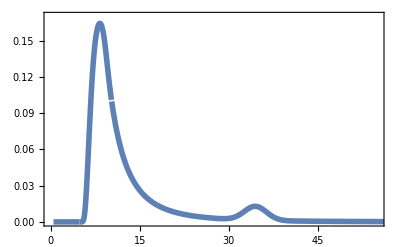

pathOut/plotArrowsMerger.pdf

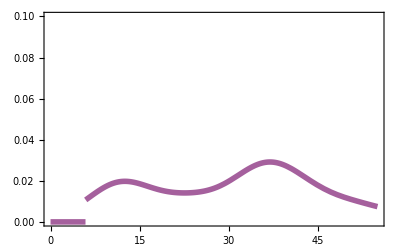

pathOut/plotArrowsObs.pdf

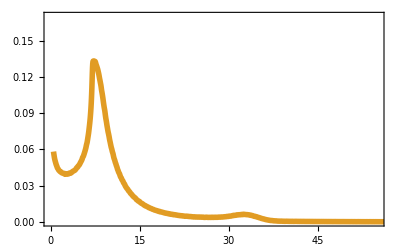

pathOut/plotArrowsCCBH.pdf

```mathematica
smooth = SmoothKernelDistribution[mXzDataForPlotting[[All,2]] /. Around[x_,y_] ->  x,
  5, 
  InterpolationPoints -> 10^5, 
  MaxExtraBandwidths -> {0,0}, (*This slightly extends the profile beyond data (about 0.1 solar mass). 
  It is only used for the plot. Use {0,0} for no extension.*)
  PerformanceGoal->"Quality"
];


plotArrowsMerger = Plot[
  {PDF[𝒟plp, x]}, 
  {x,0.5,100}, 
  PlotRange-> {{0,55}, {0,0.17}},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 22],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotPoints->2700,
  MaxRecursion->0,
  PlotStyle->{{Thickness[0.01], ColorData[97, "ColorList"][[1]]}}
]

exportOut["plotArrowsMerger.pdf", plotArrowsMerger]

plotArrowsObs = Plot[
  PDF[smooth, m], {m, 0, 55},
  PlotRange->{{0,55}, {0,.10}},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 22],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotStyle->{{Thickness[0.01], ColorData[97, "ColorList"][[9]]}}
]

exportOut["plotArrowsObs.pdf", plotArrowsObs]

plotArrowsCCBH = Plot[
  {PDF[𝒟M1Formation[0.4], x]}, 
  {x,0.5,100}, 
  PlotRange-> {{0,55}, {0,0.17}},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 22],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotPoints->2700,
  MaxRecursion->0,
  PlotStyle->{{Thickness[0.01], ColorData[97, "ColorList"][[2]]}}
]

exportOut["plotArrowsCCBH.pdf", plotArrowsCCBH]
```